```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ManualLabel=Function[{aud,durr},
Print[AudioPlot[aud]];
(*Split th audio*)
fragments=AudioPartition[aud,durr];
(*Manual label*)
labels=Table[
AudioPlay[f];
label=InputString[{f,AudioPlot[f],"Label:"}];
StringSplit[label,","],
{f,fragments}
];
(*Join fragments with labels*)
Thread[Rule[fragments,labels]]
];
```

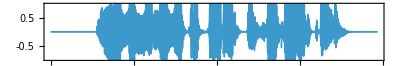

```mathematica
aud=Import["./Resources/aud_5.mp3","Audio"] ;
labels=ManualLabel[aud,Quantity[100,"Milliseconds"]];
```

```mathematica
Length[labels]
```

32

```mathematica
colorMap=<|"S"->Blue,"U"->Red,"V"->Green|>;

plots=Table[
color=If[Length[label[[2]]]>1,
Blend[Lookup[colorMap,#,Black]&/@label[[2]]],
Lookup[colorMap,label[[2,1]]]];

AudioPlot[label[[1]],PlotStyle->{color}]
,{label,labels}];

plots=Table[GraphicsGrid[{plotGroup},Spacings->0],{plotGroup,Partition[plots,UpTo[3]]}];
```

```mathematica
Table[Export["./Resources/time_aud_5_"<>ToString[i]<>".png",Rasterize[plots[[i]]]],{i,1,Length[plots]}]
```

{./Resources/time_aud_5_1.png,./Resources/time_aud_5_2.png,./Resources/time_aud_5_3.png,./Resources/time_aud_5_4.png,./Resources/time_aud_5_5.png,./Resources/time_aud_5_6.png,./Resources/time_aud_5_7.png,./Resources/time_aud_5_8.png,./Resources/time_aud_5_9.png,./Resources/time_aud_5_10.png,./Resources/time_aud_5_11.png}

```mathematica
aud1=Import["./Resources/aud_1.mp3","Audio"];
aud2=Import["./Resources/aud_2.mp3","Audio"];
aud3=Import["./Resources/aud_3.mp3","Audio"];
aud4=Import["./Resources/aud_4.mp3","Audio"];
aud5=Import["./Resources/aud_5.mp3","Audio"];
audios={aud1,aud2,aud3,aud4,aud5};
```

{,,,,}

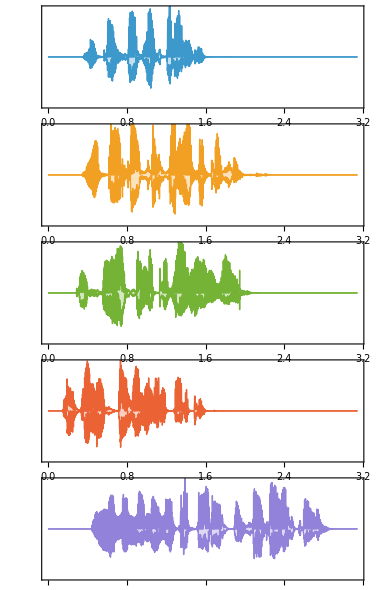

```mathematica
timeAudios=AudioPlot[audios,PlotRange->{All,{-0.5,0.5}},FillingStyle->Opacity[.3],MaxPlotPoints->2000]
Export["./Resources/time_audios.png",timeAudios];
```

```mathematica
audio=aud5;
```

```mathematica
fs=AudioSampleRate[audio][[1]];
wideband=Spectrogram[audio,
Round[15/1000*fs],
Round[1/1000*fs],
ColorFunction->Hue
]

narrowband=Spectrogram[audio,
Round[50/1000*fs],
Round[1/1000*fs],
ColorFunction->Hue
]

Export["./Resources/wide_5.png",wideband];
Export["./Resources/narrow_5.png",narrowband];
```

-Graphics-

-Graphics-